```mathematica
(* Fonctions qui déterminent si un point à coordonnées entières appartien ou non à la surface discrète *)

(* test pour appartenance à une surface sans tunnels 18-connexes *)
inNaif3D[grev_,x_,y_,z_]:=Module[{f1,f2,f3,f4,f5,f6,res}, 
f1=1.0*grev[x+0.5,y,z]; 
f2=1.0*grev[x-0.5,y,z]; 
f3=1.0*grev[x,y-0.5,z]; 
f4=1.0*grev[x,y+0.5,z]; 
f5=1.0*grev[x,y,z+0.5]; 
f6=1.0*grev[x,y,z-0.5]; 
And[Min[f1,f2,f3,f4,f5,f6]<=0,
Max[f1,f2,f3,f4,f5,f6]>=0]
];

(* test pour appartenance à une surface sans tunnels 26-connexes *)
inInter3D[grev_,x_,y_,z_]:=Module[{f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,res}, 
f1=1.0*grev[x+0.5,y+0.5,z]; 
f2=1.0*grev[x-0.5,y+0.5,z]; 
f3=1.0*grev[x+0.5,y-0.5,z]; 
f4=1.0*grev[x-0.5,y-0.5,z]; 
f5=1.0*grev[x+0.5,y,z+0.5]; 
f6=1.0*grev[x+0.5,y,z-0.5]; 
f7=1.0*grev[x-0.5,y,z+0.5]; 
f8=1.0*grev[x-0.5,y,z-0.5]; 
f9=1.0*grev[x,y+0.5,z+0.5]; 
f10=1.0*grev[x,y+0.5,z-0.5]; 
f11=1.0*grev[x,y-0.5,z+0.5]; 
f12=1.0*grev[x,y-0.5,z-0.5]; 
And[Min[f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12]<=0,
Max[f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12]>=0]
];

(* test pour appartenance à une surface sans tunnels *)
inSuper3D[grev_,x_,y_,z_]:=Module[{f1,f2,f3,f4,f5,f6,f7,f8,res}, 
f1=1.0*grev[x+0.5,y+0.5,z+0.5]; 
f2=1.0*grev[x+0.5,y+0.5,z-0.5]; 
f3=1.0*grev[x+0.5,y-0.5,z+0.5]; 
f4=1.0*grev[x+0.5,y-0.5,z-0.5]; 
f5=1.0*grev[x-0.5,y+0.5,z+0.5]; 
f6=1.0*grev[x-0.5,y+0.5,z-0.5]; 
f7=1.0*grev[x-0.5,y-0.5,z+0.5]; 
f8=1.0*grev[x-0.5,y-0.5,z-0.5]; 
And[Min[f1,f2,f3,f4,f5,f6,f7,f8]<=0,
Max[f1,f2,f3,f4,f5,f6,f7,f8]>=0]
];

(* Surface avec tunnels 18-connexes - connexité par arête *)
revolutionNaif[grevol_,xint_,yint_,zint_]:=Module[{x,y,z,listpoint},listpoint={};
For[x=xint[[1]],x≤xint[[2]],x++,
For[y=yint[[1]],y≤yint[[2]],y++,
For[z=zint[[1]],z≤zint[[2]],z++,
If[inNaif3D[grevol,x,y,z],
AppendTo[listpoint,{x,y,z}]];
]]];
listpoint];

(* Surface avec tunnels 26-connexes - connexité par face *)
revolutionInter[grevol_,xint_,yint_,zint_]:=Module[{x,y,z,listpoint},listpoint={};
For[x=xint[[1]],x≤xint[[2]],x++,
For[y=yint[[1]],y≤yint[[2]],y++,
For[z=zint[[1]],z≤zint[[2]],z++,
If[inInter3D[grevol,x,y,z],
AppendTo[listpoint,{x,y,z}]];
]]];
listpoint];

(* Surface sans tunnels - connexité par face *)
revolutionSuper[grevol_,xint_,yint_,zint_]:=Module[{x,y,z,listpoint},listpoint={};
For[x=xint[[1]],x≤xint[[2]],x++,
For[y=yint[[1]],y≤yint[[2]],y++,
For[z=zint[[1]],z≤zint[[2]],z++,
If[inSuper3D[grevol,x,y,z],
AppendTo[listpoint,{x,y,z}]];
]]];
listpoint];

(* Affichage d'une liste de points sous la forme de cubes *)
cube[pt_,vox_]:=Cuboid[pt-{vox,vox,vox},pt+{vox,vox,vox}];

affichelp[listept_,xint_,yint_,zint_,vox_]:=Module[{res,i,len,x0,x1,y0,y1,z0,z1,x,y,z},len=Length[listept]; res={Red};
{x0,x1}=xint;{y0,y1}=yint; {z0,z1}=zint;
For[i=1,i≤len,i++,
{x,y,z}=listept[[i]];
If[x≥x0 && x≤x1 && y≥y0 && y≤y1 && z≥z0 && z≤z1,
AppendTo[res,cube[listept[[i]],vox]]]];
Graphics3D[res]];

(* Algo pour visualiser une fonction 2D : en l'occurrence la courbe de révolution *)
(* On considère dans cet exemple que la courbe de révolution est située entre [-1,1]x[-1,1]
avec comme centre de révolution le point (0,0) dans le plan XY *)
view[f_]:=RegionPlot[f[x,y]<0,{x,-1,1},{y,-1,1}];
```

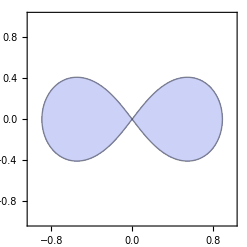
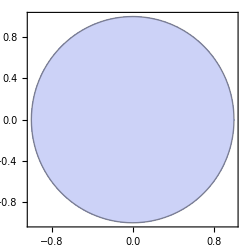
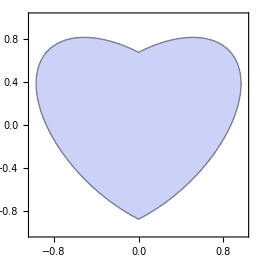
```mathematica
(* Exemple de courbe de révolutions :
xy[x_,y_]:=(0.25*x^2+0.15*y^2)^2-0.2*(0.25*x^2-0.15*y^2);
   view[xy]
-Graphics-
   xy[x_,y_] := x^2 + y^2 -1.0;
   view[xy]
-Graphics-
xy[x_,y_]:=(y-0.5*Abs[x]+0.1)^2+(0.8*x)^2-0.6;
   view[xy]
-Graphics-

*)
```

```mathematica
r[z_]:=Sin[z/9.0]*10.0+14.0;
xy[x_,y_]:=(y-0.5*Abs[x]+0.1)^2+(0.8*x)^2-0.6;
grevol[x_,y_,z_]:=xy[x/r[z],y/r[z]];
lp1=revolutionNaif[grevol,{-40,40},{-40,40},{0,50}];
lp2=revolutionInter[grevol,{-40,40},{-40,40},{0,50}];
lp3=revolutionSuper[grevol,{-40,40},{-40,40},{0,50}];
```

```mathematica
affichelp[lp1,{-40,40},{-40,40},{0,50},0.5]
affichelp[lp2,{-40,40},{-40,40},{0,50},0.5]
affichelp[lp3,{-40,40},{-40,40},{0,50},0.5]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-